```mathematica
(* 2018-01-01 candidate *)
```

```mathematica
√(1-(7+2 √5)/29.0)+I Sqrt[(7+2 √5)/29.0];
ArcTan[Sqrt[(7+2 √5)/29]/√(1-(7+2 √5)/29)]/2/Pi//FullSimplify;
```

```mathematica
a=-ArcCot[1-√5]/(2 π);
X=1/4 √(8-√(50-6 √5))+I 1/4 √(8+√(50-6 √5));
Z=((-1+ⅈ)-(-1)^(3/10)+(-1)^(4/5)-X+ⅈ Conjugate[X])/(1-ⅈ X^2);
W=-I Z X^2;

T=({{1, 1, 1, 1, 1, 1, 1, 1}, {1, W, Z, X, -I/X, Exp[Pi I 3/10], -I, Exp[Pi I 9/5]}, {1, -X, I/X, -I/Z, 1/W Exp[(3 Pi I)/2], Exp[Pi I 13/10], -I, Exp[Pi I 4/5]}, {1, Z Exp[(I Pi)/5], W Exp[(I Pi)/5], -I/X Exp[(I Pi)/5], X Exp[(I Pi)/5], Exp[Pi I 17/10], +I, Exp[Pi I 1/5]}, {1, -I/X Exp[(I Pi)/5], X Exp[(I Pi)/5], I/W Exp[(I Pi)/5], -I/Z Exp[(6 Pi I)/5], Exp[Pi I 7/10], +I, Exp[Pi I 6/5]}, {1, Exp[2 Pi I a], Exp[2 Pi I (a+1/2)], Exp[2 Pi I (1/2-a)], Exp[2 Pi I (1-a)], +1, -1, -1}, {1, Exp[2 Pi I (a+1/10)], Exp[2 Pi I (a+3/5)], Exp[2 Pi I (11/10-a)], Exp[2 Pi I (3/5-a)], -1, +1, -1}, {1, Exp[Pi I 1/5], Exp[Pi I 1/5], Exp[Pi I 6/5], Exp[Pi I 6/5], -1, -1, +1}});
T.ConjugateTranspose[T]//MatrixForm//N//Chop
```

(8. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 8. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 8. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 8. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 8. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 8. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 8. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.)

```mathematica
(* defect of a unitary matrix *)
(* it is recommended to call it with Numerical values: UnitaryDefect[N[...]] *)
UnitaryDefect[M_]:=Module[{d=Dimensions[M][[1]],R,T},
T=Table[0,{d},{d}];
R=Flatten[Table[Flatten[ReplacePart[T,{i->M[[i]] Conjugate[M[[j]]],j->-M[[i]] Conjugate[M[[j]]]}]],{i,1,d-1},{j,i+1,d}],1];
(d-1)^2-MatrixRank[Join[Re[R],Im[R]]]]
```

```mathematica
(* split form *)
```

```mathematica
α=Arg[Sqrt[(22-2 √5)/29]+I Sqrt[(7+2 √5)/29]]//FullSimplify; (* - ArcCot[1 - √5]*)
Subscript[c, 1]=1/4 √(8-√(50-6 √5))+I 1/4 √(8+√(50-6 √5));
Subscript[c, 2]=((-1+ⅈ)-(-1)^(3/10)+(-1)^(4/5)-Subscript[c, 1]+I/Subscript[c, 1])/(1-I Subscript[c, 1]^2);
Subscript[c, 3]=-I Subscript[c, 2] Subscript[c, 1]^2;
T=({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 3, 15, 18}, {0, 0, 0, 0, 0, 13, 15, 8}, {0, 2, 2, 2, 2, 17, 5, 2}, {0, 2, 2, 2, 2, 7, 5, 12}, {0, 0, 0, 0, 0, 0, 10, 10}, {0, 2, 2, 12, 12, 10, 0, 10}, {0, 2, 2, 12, 12, 10, 10, 0}});
Subscript[T, c]=({{1, 1, 1, 1, 1, 1, 1, 1}, {1, Subscript[c, 3], Subscript[c, 2], Subscript[c, 1], -I/Subscript[c, 1], 1, 1, 1}, {1, -Subscript[c, 1], I/Subscript[c, 1], -I/Subscript[c, 2], -I/Subscript[c, 3], 1, 1, 1}, {1, Subscript[c, 2], Subscript[c, 3], -I/Subscript[c, 1], Subscript[c, 1], 1, 1, 1}, {1, -I/Subscript[c, 1], Subscript[c, 1], I/Subscript[c, 3], I/Subscript[c, 2], 1, 1, 1}, {1, ⅇ^(I α), -ⅇ^(I α), -ⅇ^(-I α), ⅇ^(-I α), 1, 1, 1}, {1, ⅇ^(I α), -ⅇ^(I α), -ⅇ^(-I α), ⅇ^(-I α), 1, 1, 1}, {1, 1, 1, 1, 1, 1, 1, 1}});
Subscript[T, 8]=Subscript[T, c]*Exp[I Pi T 1/10];
Subscript[T, 8]//MatrixForm//N
Subscript[T, 8].ConjugateTranspose[Subscript[T, 8]]//MatrixForm//N//Chop
UnitaryDefect[N[Subscript[T, 8]]]
```

(1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | -0.948145-0.317838 ⅈ | -0.860872+0.508821 ⅈ | 0.349246+0.937031 ⅈ | -0.937031-0.349246 ⅈ | 0.587785+0.809017 ⅈ | 0.-1. ⅈ | 0.809017-0.587785 ⅈ
1. | -0.349246-0.937031 ⅈ | 0.937031+0.349246 ⅈ | -0.508821+0.860872 ⅈ | 0.317838+0.948145 ⅈ | -0.587785-0.809017 ⅈ | 0.-1. ⅈ | -0.809017+0.587785 ⅈ
1. | -0.995538-0.0943628 ⅈ | -0.580245-0.814442 ⅈ | -0.552793-0.833319 ⅈ | -0.268227+0.963356 ⅈ | 0.587785-0.809017 ⅈ | 0.+1. ⅈ | 0.809017+0.587785 ⅈ
1. | -0.552793-0.833319 ⅈ | -0.268227+0.963356 ⅈ | 0.300169-0.953886 ⅈ | 0.917653-0.397382 ⅈ | -0.587785+0.809017 ⅈ | 0.+1. ⅈ | -0.809017-0.587785 ⅈ
1. | 0.777438+0.62896 ⅈ | -0.777438-0.62896 ⅈ | -0.777438+0.62896 ⅈ | 0.777438-0.62896 ⅈ | 1. | -1. | -1.
1. | 0.259267+0.965806 ⅈ | -0.259267-0.965806 ⅈ | 0.998654-0.0518732 ⅈ | -0.998654+0.0518732 ⅈ | -1. | 1. | -1.
1. | 0.809017+0.587785 ⅈ | 0.809017+0.587785 ⅈ | -0.809017-0.587785 ⅈ | -0.809017-0.587785 ⅈ | -1. | -1. | 1.)

(8. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 8. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 8. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 8. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 8. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 8. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 8. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.)

3

```mathematica
(* another candidate expressed in the analytical form *)
(* with fixed unities at Subscript[T, 7,2] and Subscript[T, 7,3] *)
```

```mathematica
x=1/2 (1-√5+√(2 (-2+√5)))-I √(1/2+√(-11+5 √5));
(*t=(-1+(-1)^(7/10)+(1+ⅈ) (1+(-1)^(7/10)) x)/((-ⅈ+(-1)^(1/5)) x);*)
t=I-1-Cot[3/20 Pi] 1/x;
(*z=((1+ⅈ) (ⅈ+(-1)^(4/5))+(-1+(-1)^(3/10)) x)/(1+(-1)^(3/10));*)
z=I-1+I Tan[3/20 Pi]x;
(*a=1-√5+√(5-2 √5)-(1-ⅈ)x;*)
a=-Tan[3/20 Pi]-(1-I)x;
T690=({{1, 1, 1, 1, 1, 1, 1, 1}, {1, +x, I x Exp[I Pi 4/5], z, -I z Exp[I Pi 4/5], Exp[I Pi 3/10], -I, Exp[I Pi 9/5]}, {1, -I/x, -1/x Exp[I Pi 4/5], t, +I t Exp[I Pi 4/5], Exp[I Pi 13/10], -I, Exp[I Pi 4/5]}, {1, -I x, x Exp[I Pi 1/5], z Exp[I Pi 1/2], -I z Exp[I Pi 7/10], Exp[I Pi 17/10], +I, Exp[I Pi 1/5]}, {1, -1/x, I/x Exp[I Pi 1/5], I t, -t Exp[I Pi 1/5], Exp[I Pi 7/10], +I, Exp[I Pi 6/5]}, {1, +a, -a, -1/a, +1/a, +1, -1, -1}, {1, -1, +1, -1/a^2, +1/a^2, -1, +1, -1}, {1, -1/a, -1/a, +1/a, +1/a, -1, -1, +1}});
T690.ConjugateTranspose[T690]//MatrixForm//N//Chop
T690//MatrixForm//N
```

(8. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 8. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 8. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 8. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 8. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 8. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 8. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.)

(1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | -0.274473-0.961595 ⅈ | -0.616615+0.787265 ⅈ | -0.510043+0.860149 ⅈ | -0.995671+0.0929494 ⅈ | 0.587785+0.809017 ⅈ | 0.-1. ⅈ | 0.809017-0.587785 ⅈ
1. | 0.961595+0.274473 ⅈ | 0.343158+0.939278 ⅈ | -0.461316-0.887236 ⅈ | -0.446634+0.894717 ⅈ | -0.587785-0.809017 ⅈ | 0.-1. ⅈ | -0.809017+0.587785 ⅈ
1. | -0.961595+0.274473 ⅈ | 0.343158-0.939278 ⅈ | -0.860149-0.510043 ⅈ | -0.918216+0.396079 ⅈ | 0.587785-0.809017 ⅈ | 0.+1. ⅈ | 0.809017+0.587785 ⅈ
1. | 0.274473-0.961595 ⅈ | -0.616615-0.787265 ⅈ | 0.887236-0.461316 ⅈ | -0.148292+0.988944 ⅈ | -0.587785+0.809017 ⅈ | 0.+1. ⅈ | -0.809017-0.587785 ⅈ
1. | 0.726543+0.687121 ⅈ | -0.726543-0.687121 ⅈ | -0.726543+0.687121 ⅈ | 0.726543-0.687121 ⅈ | 1. | -1. | -1.
1. | -1. | 1. | -0.0557281+0.998446 ⅈ | 0.0557281-0.998446 ⅈ | -1. | 1. | -1.
1. | -0.726543+0.687121 ⅈ | -0.726543+0.687121 ⅈ | 0.726543-0.687121 ⅈ | 0.726543-0.687121 ⅈ | -1. | -1. | 1.)

```mathematica
(********************************************** FULL FORMULAS ************)
```

```mathematica
(* 20180103 non-affine family of CHM of size 8 and of generic defect=3 - original file (big mess!) *)
(* Mathematica 8.0.0 *)
```

```mathematica
(*y=((2+2 ⅈ) √(1-√5+ⅈ √(2 (5+√5)))-(4-4 ⅈ) x^2-(1-ⅈ) Conjugate[√(4 (-1+√5+ⅈ √(2 (5+√5)))+(1+ⅈ) Conjugate[x] ((-40+40 ⅈ)+(24-8 ⅈ) √5-√(50-10 √5)+(4+8 ⅈ) √(5 (5-2 √5))+(7+4 ⅈ) √(10-2 √5)+√(2 (5+√5)) ((-5+16 ⅈ)+(1-12 ⅈ) √5)+(1+ⅈ) Conjugate[x] ((180-36 ⅈ)-(68-28 ⅈ) √5+17 √(50-10 √5)-(9-16 ⅈ) √(10-2 √5)+((15-20 ⅈ)-17 √5) √(2 (5+√5))-(4+4 ⅈ) Conjugate[x] (5-3 √5-(2-ⅈ) √(10-2 √5)+2 √(2 (5+√5))+(1+ⅈ) Conjugate[x]))))]-2 x ((1-4 ⅈ)+√5+Root[80+20 #1^2+#1^4&,1]))/(4 ((-2-2 ⅈ)+2 √5+√(10-2 √5)-√(2 (5+√5))+(2-2 ⅈ) x));*)
(*z=(x ((-1+ⅈ)+(1+ⅈ) (-1)^(4/5)-x-y))/(x-y);*)
T333=({{1, 1, 1, 1, 1, 1, 1, 1}, {1, x, y, z, -(y z)/x, Exp[Pi I 3/10], -I, Exp[Pi I 9/5]}, {1, -Exp[I Pi 2α]/y Exp[I Pi 4/5], Exp[I Pi 2α]/x Exp[I Pi 4/5], x/a^2 Exp[I Pi 2 α]/(y z)Exp[I Pi 4/5], 1/a^2 Exp[I Pi 2 α]/z Exp[I Pi 4/5], Exp[Pi I 13/10], -I, Exp[Pi I 4/5]}, {1, y Exp[I Pi 1/5], x Exp[I Pi 1/5], -(y z)/x Exp[I Pi 1/5], z Exp[I Pi 1/5], Exp[Pi I 17/10], +I, Exp[Pi I 1/5]}, {1, Exp[I Pi 2α]/x, -Exp[I Pi 2α]/y, 1/a^2 Exp[I Pi 2 α]/z, x/a^2 Exp[I Pi 2 α]/(y z), Exp[Pi I 7/10], +I, Exp[Pi I 6/5]}, {1, a, -a, -1/a, 1/a, +1, -1, -1}, {1, Exp[I Pi 2α], -Exp[I Pi 2α], 1/a^2 Exp[I Pi 2 α], -1/a^2 Exp[I Pi 2 α], -1, +1, -1}, {1, 1/a Exp[I Pi 2 α], 1/a Exp[I Pi 2 α], -1/a Exp[I Pi 2 α], -1/a Exp[I Pi 2 α], -1, -1, +1}});
(*Simplify[T333.ConjugateTranspose[T333],α∈Reals]//MatrixForm//Chop*)
```

```mathematica
T333.ConjugateTranspose[T333]//MatrixForm//Chop
```

(8 | (1+ⅈ)+ⅇ^((ⅈ π)/5)+ⅇ^(-(3 ⅈ π)/10)+Conjugate[x]+Conjugate[y]+Conjugate[z]-Conjugate[y z]/Conjugate[x] | (1+ⅈ)+ⅇ^((7 ⅈ π)/10)+ⅇ^(-(4 ⅈ π)/5)+ⅇ^(-(4 ⅈ π)/5-2 ⅈ π Conjugate[α])/Conjugate[x]-ⅇ^(-(4 ⅈ π)/5-2 ⅈ π Conjugate[α])/Conjugate[y]+ⅇ^(-(4 ⅈ π)/5-2 ⅈ π Conjugate[α])/(Conjugate[a]^2 Conjugate[z])+(ⅇ^(-(4 ⅈ π)/5-2 ⅈ π Conjugate[α]) Conjugate[x])/(Conjugate[a]^2 Conjugate[y] Conjugate[z]) | (1-ⅈ)+ⅇ^(-(ⅈ π)/5)+ⅇ^((3 ⅈ π)/10)+ⅇ^(-(ⅈ π)/5) Conjugate[x]+ⅇ^(-(ⅈ π)/5) Conjugate[y]+ⅇ^(-(ⅈ π)/5) Conjugate[z]-(ⅇ^(-(ⅈ π)/5) Conjugate[y z])/Conjugate[x] | (1-ⅈ)+ⅇ^(-(7 ⅈ π)/10)+ⅇ^((4 ⅈ π)/5)+ⅇ^(-2 ⅈ π Conjugate[α])/Conjugate[x]-ⅇ^(-2 ⅈ π Conjugate[α])/Conjugate[y]+ⅇ^(-2 ⅈ π Conjugate[α])/(Conjugate[a]^2 Conjugate[z])+(ⅇ^(-2 ⅈ π Conjugate[α]) Conjugate[x])/(Conjugate[a]^2 Conjugate[y] Conjugate[z]) | 0 | 0 | 0
(1-ⅈ)+ⅇ^(-(ⅈ π)/5)+ⅇ^((3 ⅈ π)/10)+x+y+z-(y z)/x | 4+x Conjugate[x]+y Conjugate[y]+z Conjugate[z]+(y z Conjugate[y z])/(x Conjugate[x]) | (ⅇ^(-(4 ⅈ π)/5-2 ⅈ π Conjugate[α]) y)/Conjugate[x]-(ⅇ^(-(4 ⅈ π)/5-2 ⅈ π Conjugate[α]) x)/Conjugate[y]-(ⅇ^(-(4 ⅈ π)/5-2 ⅈ π Conjugate[α]) y z)/(x Conjugate[a]^2 Conjugate[z])+(ⅇ^(-(4 ⅈ π)/5-2 ⅈ π Conjugate[α]) z Conjugate[x])/(Conjugate[a]^2 Conjugate[y] Conjugate[z]) | ⅇ^(-(2 ⅈ π)/5)+ⅇ^((3 ⅈ π)/5)+ⅇ^(-(ⅈ π)/5) y Conjugate[x]+ⅇ^(-(ⅈ π)/5) x Conjugate[y]-(ⅇ^(-(ⅈ π)/5) y z Conjugate[z])/x-(ⅇ^(-(ⅈ π)/5) z Conjugate[y z])/Conjugate[x] | ⅇ^(-(2 ⅈ π)/5)+ⅇ^((3 ⅈ π)/5)+(ⅇ^(-2 ⅈ π Conjugate[α]) x)/Conjugate[x]-(ⅇ^(-2 ⅈ π Conjugate[α]) y)/Conjugate[y]+(ⅇ^(-2 ⅈ π Conjugate[α]) z)/(Conjugate[a]^2 Conjugate[z])-(ⅇ^(-2 ⅈ π Conjugate[α]) y z Conjugate[x])/(x Conjugate[a]^2 Conjugate[y] Conjugate[z]) | (1+ⅈ)-ⅇ^(-(ⅈ π)/5)+ⅇ^((3 ⅈ π)/10)-z/Conjugate[a]-(y z)/(x Conjugate[a])+x Conjugate[a]-y Conjugate[a] | (1-ⅈ)-ⅇ^(-(ⅈ π)/5)-ⅇ^((3 ⅈ π)/10)+ⅇ^(-2 ⅈ π Conjugate[α]) x-ⅇ^(-2 ⅈ π Conjugate[α]) y+(ⅇ^(-2 ⅈ π Conjugate[α]) z)/Conjugate[a]^2+(ⅇ^(-2 ⅈ π Conjugate[α]) y z)/(x Conjugate[a]^2) | (1+ⅈ)+ⅇ^(-(ⅈ π)/5)-ⅇ^((3 ⅈ π)/10)+(ⅇ^(-2 ⅈ π Conjugate[α]) x)/Conjugate[a]+(ⅇ^(-2 ⅈ π Conjugate[α]) y)/Conjugate[a]-(ⅇ^(-2 ⅈ π Conjugate[α]) z)/Conjugate[a]+(ⅇ^(-2 ⅈ π Conjugate[α]) y z)/(x Conjugate[a])
(1-ⅈ)+ⅇ^(-(7 ⅈ π)/10)+ⅇ^((4 ⅈ π)/5)+ⅇ^((4 ⅈ π)/5+2 ⅈ π α)/x-ⅇ^((4 ⅈ π)/5+2 ⅈ π α)/y+ⅇ^((4 ⅈ π)/5+2 ⅈ π α)/(a^2 z)+(ⅇ^((4 ⅈ π)/5+2 ⅈ π α) x)/(a^2 y z) | -(ⅇ^((4 ⅈ π)/5+2 ⅈ π α) Conjugate[x])/y+(ⅇ^((4 ⅈ π)/5+2 ⅈ π α) Conjugate[y])/x+(ⅇ^((4 ⅈ π)/5+2 ⅈ π α) x Conjugate[z])/(a^2 y z)-(ⅇ^((4 ⅈ π)/5+2 ⅈ π α) Conjugate[y z])/(a^2 z Conjugate[x]) | 4+ⅇ^(2 ⅈ π α-2 ⅈ π Conjugate[α])/(x Conjugate[x])+ⅇ^(2 ⅈ π α-2 ⅈ π Conjugate[α])/(y Conjugate[y])+ⅇ^(2 ⅈ π α-2 ⅈ π Conjugate[α])/(a^2 z Conjugate[a]^2 Conjugate[z])+(ⅇ^(2 ⅈ π α-2 ⅈ π Conjugate[α]) x Conjugate[x])/(a^2 y z Conjugate[a]^2 Conjugate[y] Conjugate[z]) | ⅇ^(-(2 ⅈ π)/5)+ⅇ^((3 ⅈ π)/5)+(ⅇ^((3 ⅈ π)/5+2 ⅈ π α) Conjugate[x])/x-(ⅇ^((3 ⅈ π)/5+2 ⅈ π α) Conjugate[y])/y+(ⅇ^((3 ⅈ π)/5+2 ⅈ π α) Conjugate[z])/(a^2 z)-(ⅇ^((3 ⅈ π)/5+2 ⅈ π α) x Conjugate[y z])/(a^2 y z Conjugate[x]) | ⅇ^(-(2 ⅈ π)/5)+ⅇ^((3 ⅈ π)/5)-ⅇ^((4 ⅈ π)/5+2 ⅈ π α-2 ⅈ π Conjugate[α])/(y Conjugate[x])-ⅇ^((4 ⅈ π)/5+2 ⅈ π α-2 ⅈ π Conjugate[α])/(x Conjugate[y])+(ⅇ^((4 ⅈ π)/5+2 ⅈ π α-2 ⅈ π Conjugate[α]) x)/(a^2 y z Conjugate[a]^2 Conjugate[z])+(ⅇ^((4 ⅈ π)/5+2 ⅈ π α-2 ⅈ π Conjugate[α]) Conjugate[x])/(a^2 z Conjugate[a]^2 Conjugate[y] Conjugate[z]) | (1+ⅈ)+ⅇ^(-(7 ⅈ π)/10)-ⅇ^((4 ⅈ π)/5)+ⅇ^((4 ⅈ π)/5+2 ⅈ π α)/(a^2 z Conjugate[a])-(ⅇ^((4 ⅈ π)/5+2 ⅈ π α) x)/(a^2 y z Conjugate[a])-(ⅇ^((4 ⅈ π)/5+2 ⅈ π α) Conjugate[a])/x-(ⅇ^((4 ⅈ π)/5+2 ⅈ π α) Conjugate[a])/y | (1-ⅈ)-ⅇ^(-(7 ⅈ π)/10)-ⅇ^((4 ⅈ π)/5)-ⅇ^((4 ⅈ π)/5+2 ⅈ π α-2 ⅈ π Conjugate[α])/x-ⅇ^((4 ⅈ π)/5+2 ⅈ π α-2 ⅈ π Conjugate[α])/y-ⅇ^((4 ⅈ π)/5+2 ⅈ π α-2 ⅈ π Conjugate[α])/(a^2 z Conjugate[a]^2)+(ⅇ^((4 ⅈ π)/5+2 ⅈ π α-2 ⅈ π Conjugate[α]) x)/(a^2 y z Conjugate[a]^2) | (1+ⅈ)-ⅇ^(-(7 ⅈ π)/10)+ⅇ^((4 ⅈ π)/5)+ⅇ^((4 ⅈ π)/5+2 ⅈ π α-2 ⅈ π Conjugate[α])/(x Conjugate[a])-ⅇ^((4 ⅈ π)/5+2 ⅈ π α-2 ⅈ π Conjugate[α])/(y Conjugate[a])-ⅇ^((4 ⅈ π)/5+2 ⅈ π α-2 ⅈ π Conjugate[α])/(a^2 z Conjugate[a])-(ⅇ^((4 ⅈ π)/5+2 ⅈ π α-2 ⅈ π Conjugate[α]) x)/(a^2 y z Conjugate[a])
(1+ⅈ)+ⅇ^((ⅈ π)/5)+ⅇ^(-(3 ⅈ π)/10)+ⅇ^((ⅈ π)/5) x+ⅇ^((ⅈ π)/5) y+ⅇ^((ⅈ π)/5) z-(ⅇ^((ⅈ π)/5) y z)/x | ⅇ^((2 ⅈ π)/5)+ⅇ^(-(3 ⅈ π)/5)+ⅇ^((ⅈ π)/5) y Conjugate[x]+ⅇ^((ⅈ π)/5) x Conjugate[y]-(ⅇ^((ⅈ π)/5) y z Conjugate[z])/x-(ⅇ^((ⅈ π)/5) z Conjugate[y z])/Conjugate[x] | ⅇ^((2 ⅈ π)/5)+ⅇ^(-(3 ⅈ π)/5)+(ⅇ^(-(3 ⅈ π)/5-2 ⅈ π Conjugate[α]) x)/Conjugate[x]-(ⅇ^(-(3 ⅈ π)/5-2 ⅈ π Conjugate[α]) y)/Conjugate[y]+(ⅇ^(-(3 ⅈ π)/5-2 ⅈ π Conjugate[α]) z)/(Conjugate[a]^2 Conjugate[z])-(ⅇ^(-(3 ⅈ π)/5-2 ⅈ π Conjugate[α]) y z Conjugate[x])/(x Conjugate[a]^2 Conjugate[y] Conjugate[z]) | 4+x Conjugate[x]+y Conjugate[y]+z Conjugate[z]+(y z Conjugate[y z])/(x Conjugate[x]) | (ⅇ^((ⅈ π)/5-2 ⅈ π Conjugate[α]) y)/Conjugate[x]-(ⅇ^((ⅈ π)/5-2 ⅈ π Conjugate[α]) x)/Conjugate[y]-(ⅇ^((ⅈ π)/5-2 ⅈ π Conjugate[α]) y z)/(x Conjugate[a]^2 Conjugate[z])+(ⅇ^((ⅈ π)/5-2 ⅈ π Conjugate[α]) z Conjugate[x])/(Conjugate[a]^2 Conjugate[y] Conjugate[z]) | (1-ⅈ)-ⅇ^((ⅈ π)/5)+ⅇ^(-(3 ⅈ π)/10)+(ⅇ^((ⅈ π)/5) z)/Conjugate[a]+(ⅇ^((ⅈ π)/5) y z)/(x Conjugate[a])-ⅇ^((ⅈ π)/5) x Conjugate[a]+ⅇ^((ⅈ π)/5) y Conjugate[a] | (1+ⅈ)-ⅇ^((ⅈ π)/5)-ⅇ^(-(3 ⅈ π)/10)-ⅇ^((ⅈ π)/5-2 ⅈ π Conjugate[α]) x+ⅇ^((ⅈ π)/5-2 ⅈ π Conjugate[α]) y-(ⅇ^((ⅈ π)/5-2 ⅈ π Conjugate[α]) z)/Conjugate[a]^2-(ⅇ^((ⅈ π)/5-2 ⅈ π Conjugate[α]) y z)/(x Conjugate[a]^2) | (1-ⅈ)+ⅇ^((ⅈ π)/5)-ⅇ^(-(3 ⅈ π)/10)+(ⅇ^((ⅈ π)/5-2 ⅈ π Conjugate[α]) x)/Conjugate[a]+(ⅇ^((ⅈ π)/5-2 ⅈ π Conjugate[α]) y)/Conjugate[a]-(ⅇ^((ⅈ π)/5-2 ⅈ π Conjugate[α]) z)/Conjugate[a]+(ⅇ^((ⅈ π)/5-2 ⅈ π Conjugate[α]) y z)/(x Conjugate[a])
(1+ⅈ)+ⅇ^((7 ⅈ π)/10)+ⅇ^(-(4 ⅈ π)/5)+ⅇ^(2 ⅈ π α)/x-ⅇ^(2 ⅈ π α)/y+ⅇ^(2 ⅈ π α)/(a^2 z)+(ⅇ^(2 ⅈ π α) x)/(a^2 y z) | ⅇ^((2 ⅈ π)/5)+ⅇ^(-(3 ⅈ π)/5)+(ⅇ^(2 ⅈ π α) Conjugate[x])/x-(ⅇ^(2 ⅈ π α) Conjugate[y])/y+(ⅇ^(2 ⅈ π α) Conjugate[z])/(a^2 z)-(ⅇ^(2 ⅈ π α) x Conjugate[y z])/(a^2 y z Conjugate[x]) | ⅇ^((2 ⅈ π)/5)+ⅇ^(-(3 ⅈ π)/5)-ⅇ^(-(4 ⅈ π)/5+2 ⅈ π α-2 ⅈ π Conjugate[α])/(y Conjugate[x])-ⅇ^(-(4 ⅈ π)/5+2 ⅈ π α-2 ⅈ π Conjugate[α])/(x Conjugate[y])+(ⅇ^(-(4 ⅈ π)/5+2 ⅈ π α-2 ⅈ π Conjugate[α]) x)/(a^2 y z Conjugate[a]^2 Conjugate[z])+(ⅇ^(-(4 ⅈ π)/5+2 ⅈ π α-2 ⅈ π Conjugate[α]) Conjugate[x])/(a^2 z Conjugate[a]^2 Conjugate[y] Conjugate[z]) | -(ⅇ^(-(ⅈ π)/5+2 ⅈ π α) Conjugate[x])/y+(ⅇ^(-(ⅈ π)/5+2 ⅈ π α) Conjugate[y])/x+(ⅇ^(-(ⅈ π)/5+2 ⅈ π α) x Conjugate[z])/(a^2 y z)-(ⅇ^(-(ⅈ π)/5+2 ⅈ π α) Conjugate[y z])/(a^2 z Conjugate[x]) | 4+ⅇ^(2 ⅈ π α-2 ⅈ π Conjugate[α])/(x Conjugate[x])+ⅇ^(2 ⅈ π α-2 ⅈ π Conjugate[α])/(y Conjugate[y])+ⅇ^(2 ⅈ π α-2 ⅈ π Conjugate[α])/(a^2 z Conjugate[a]^2 Conjugate[z])+(ⅇ^(2 ⅈ π α-2 ⅈ π Conjugate[α]) x Conjugate[x])/(a^2 y z Conjugate[a]^2 Conjugate[y] Conjugate[z]) | (1-ⅈ)+ⅇ^((7 ⅈ π)/10)-ⅇ^(-(4 ⅈ π)/5)-ⅇ^(2 ⅈ π α)/(a^2 z Conjugate[a])+(ⅇ^(2 ⅈ π α) x)/(a^2 y z Conjugate[a])+(ⅇ^(2 ⅈ π α) Conjugate[a])/x+(ⅇ^(2 ⅈ π α) Conjugate[a])/y | (1+ⅈ)-ⅇ^((7 ⅈ π)/10)-ⅇ^(-(4 ⅈ π)/5)+ⅇ^(2 ⅈ π α-2 ⅈ π Conjugate[α])/x+ⅇ^(2 ⅈ π α-2 ⅈ π Conjugate[α])/y+ⅇ^(2 ⅈ π α-2 ⅈ π Conjugate[α])/(a^2 z Conjugate[a]^2)-(ⅇ^(2 ⅈ π α-2 ⅈ π Conjugate[α]) x)/(a^2 y z Conjugate[a]^2) | (1-ⅈ)-ⅇ^((7 ⅈ π)/10)+ⅇ^(-(4 ⅈ π)/5)+ⅇ^(2 ⅈ π α-2 ⅈ π Conjugate[α])/(x Conjugate[a])-ⅇ^(2 ⅈ π α-2 ⅈ π Conjugate[α])/(y Conjugate[a])-ⅇ^(2 ⅈ π α-2 ⅈ π Conjugate[α])/(a^2 z Conjugate[a])-(ⅇ^(2 ⅈ π α-2 ⅈ π Conjugate[α]) x)/(a^2 y z Conjugate[a])
0 | (1-ⅈ)-ⅇ^((ⅈ π)/5)+ⅇ^(-(3 ⅈ π)/10)+a Conjugate[x]-a Conjugate[y]-Conjugate[z]/a-Conjugate[y z]/(a Conjugate[x]) | (1-ⅈ)+ⅇ^((7 ⅈ π)/10)-ⅇ^(-(4 ⅈ π)/5)-(a ⅇ^(-(4 ⅈ π)/5-2 ⅈ π Conjugate[α]))/Conjugate[x]-(a ⅇ^(-(4 ⅈ π)/5-2 ⅈ π Conjugate[α]))/Conjugate[y]+ⅇ^(-(4 ⅈ π)/5-2 ⅈ π Conjugate[α])/(a Conjugate[a]^2 Conjugate[z])-(ⅇ^(-(4 ⅈ π)/5-2 ⅈ π Conjugate[α]) Conjugate[x])/(a Conjugate[a]^2 Conjugate[y] Conjugate[z]) | (1+ⅈ)-ⅇ^(-(ⅈ π)/5)+ⅇ^((3 ⅈ π)/10)-a ⅇ^(-(ⅈ π)/5) Conjugate[x]+a ⅇ^(-(ⅈ π)/5) Conjugate[y]+(ⅇ^(-(ⅈ π)/5) Conjugate[z])/a+(ⅇ^(-(ⅈ π)/5) Conjugate[y z])/(a Conjugate[x]) | (1+ⅈ)+ⅇ^(-(7 ⅈ π)/10)-ⅇ^((4 ⅈ π)/5)+(a ⅇ^(-2 ⅈ π Conjugate[α]))/Conjugate[x]+(a ⅇ^(-2 ⅈ π Conjugate[α]))/Conjugate[y]-ⅇ^(-2 ⅈ π Conjugate[α])/(a Conjugate[a]^2 Conjugate[z])+(ⅇ^(-2 ⅈ π Conjugate[α]) Conjugate[x])/(a Conjugate[a]^2 Conjugate[y] Conjugate[z]) | 4+2/(a Conjugate[a])+2 a Conjugate[a] | 2 a ⅇ^(-2 ⅈ π Conjugate[α])-(2 ⅇ^(-2 ⅈ π Conjugate[α]))/(a Conjugate[a]^2) | 0
0 | (1+ⅈ)-ⅇ^((ⅈ π)/5)-ⅇ^(-(3 ⅈ π)/10)+ⅇ^(2 ⅈ π α) Conjugate[x]-ⅇ^(2 ⅈ π α) Conjugate[y]+(ⅇ^(2 ⅈ π α) Conjugate[z])/a^2+(ⅇ^(2 ⅈ π α) Conjugate[y z])/(a^2 Conjugate[x]) | (1+ⅈ)-ⅇ^((7 ⅈ π)/10)-ⅇ^(-(4 ⅈ π)/5)-ⅇ^(-(4 ⅈ π)/5+2 ⅈ π α-2 ⅈ π Conjugate[α])/Conjugate[x]-ⅇ^(-(4 ⅈ π)/5+2 ⅈ π α-2 ⅈ π Conjugate[α])/Conjugate[y]-ⅇ^(-(4 ⅈ π)/5+2 ⅈ π α-2 ⅈ π Conjugate[α])/(a^2 Conjugate[a]^2 Conjugate[z])+(ⅇ^(-(4 ⅈ π)/5+2 ⅈ π α-2 ⅈ π Conjugate[α]) Conjugate[x])/(a^2 Conjugate[a]^2 Conjugate[y] Conjugate[z]) | (1-ⅈ)-ⅇ^(-(ⅈ π)/5)-ⅇ^((3 ⅈ π)/10)-ⅇ^(-(ⅈ π)/5+2 ⅈ π α) Conjugate[x]+ⅇ^(-(ⅈ π)/5+2 ⅈ π α) Conjugate[y]-(ⅇ^(-(ⅈ π)/5+2 ⅈ π α) Conjugate[z])/a^2-(ⅇ^(-(ⅈ π)/5+2 ⅈ π α) Conjugate[y z])/(a^2 Conjugate[x]) | (1-ⅈ)-ⅇ^(-(7 ⅈ π)/10)-ⅇ^((4 ⅈ π)/5)+ⅇ^(2 ⅈ π α-2 ⅈ π Conjugate[α])/Conjugate[x]+ⅇ^(2 ⅈ π α-2 ⅈ π Conjugate[α])/Conjugate[y]+ⅇ^(2 ⅈ π α-2 ⅈ π Conjugate[α])/(a^2 Conjugate[a]^2 Conjugate[z])-(ⅇ^(2 ⅈ π α-2 ⅈ π Conjugate[α]) Conjugate[x])/(a^2 Conjugate[a]^2 Conjugate[y] Conjugate[z]) | -(2 ⅇ^(2 ⅈ π α))/(a^2 Conjugate[a])+2 ⅇ^(2 ⅈ π α) Conjugate[a] | 4+2 ⅇ^(2 ⅈ π α-2 ⅈ π Conjugate[α])+(2 ⅇ^(2 ⅈ π α-2 ⅈ π Conjugate[α]))/(a^2 Conjugate[a]^2) | 0
0 | (1-ⅈ)+ⅇ^((ⅈ π)/5)-ⅇ^(-(3 ⅈ π)/10)+(ⅇ^(2 ⅈ π α) Conjugate[x])/a+(ⅇ^(2 ⅈ π α) Conjugate[y])/a-(ⅇ^(2 ⅈ π α) Conjugate[z])/a+(ⅇ^(2 ⅈ π α) Conjugate[y z])/(a Conjugate[x]) | (1-ⅈ)-ⅇ^((7 ⅈ π)/10)+ⅇ^(-(4 ⅈ π)/5)+ⅇ^(-(4 ⅈ π)/5+2 ⅈ π α-2 ⅈ π Conjugate[α])/(a Conjugate[x])-ⅇ^(-(4 ⅈ π)/5+2 ⅈ π α-2 ⅈ π Conjugate[α])/(a Conjugate[y])-ⅇ^(-(4 ⅈ π)/5+2 ⅈ π α-2 ⅈ π Conjugate[α])/(a Conjugate[a]^2 Conjugate[z])-(ⅇ^(-(4 ⅈ π)/5+2 ⅈ π α-2 ⅈ π Conjugate[α]) Conjugate[x])/(a Conjugate[a]^2 Conjugate[y] Conjugate[z]) | (1+ⅈ)+ⅇ^(-(ⅈ π)/5)-ⅇ^((3 ⅈ π)/10)+(ⅇ^(-(ⅈ π)/5+2 ⅈ π α) Conjugate[x])/a+(ⅇ^(-(ⅈ π)/5+2 ⅈ π α) Conjugate[y])/a-(ⅇ^(-(ⅈ π)/5+2 ⅈ π α) Conjugate[z])/a+(ⅇ^(-(ⅈ π)/5+2 ⅈ π α) Conjugate[y z])/(a Conjugate[x]) | (1+ⅈ)-ⅇ^(-(7 ⅈ π)/10)+ⅇ^((4 ⅈ π)/5)+ⅇ^(2 ⅈ π α-2 ⅈ π Conjugate[α])/(a Conjugate[x])-ⅇ^(2 ⅈ π α-2 ⅈ π Conjugate[α])/(a Conjugate[y])-ⅇ^(2 ⅈ π α-2 ⅈ π Conjugate[α])/(a Conjugate[a]^2 Conjugate[z])-(ⅇ^(2 ⅈ π α-2 ⅈ π Conjugate[α]) Conjugate[x])/(a Conjugate[a]^2 Conjugate[y] Conjugate[z]) | 0 | 0 | 4+(4 ⅇ^(2 ⅈ π α-2 ⅈ π Conjugate[α]))/(a Conjugate[a]))

```mathematica
(* get z from the element MATRIX[1,2] of above... *)
Solve[(1-ⅈ)+ⅇ^(-(ⅈ π)/5)+ⅇ^((3 ⅈ π)/10)+x+y+z-(y z)/x==0,z]//FullSimplify
```

{{z→-(x ((-1-ⅈ) (ⅈ+(-1)^(4/5))+x+y))/(x-y)}}

```mathematica
Solve[(1-ⅈ)-ⅇ^((ⅈ π)/5)+ⅇ^(-(3 ⅈ π)/10)+a Conjugate[x]-(Conjugate[x] ((-1-ⅈ)+(1-ⅈ) (1/4 (-1-√5)-ⅈ √(5/8-(√5)/8))-Conjugate[x]-Conjugate[y]))/(a (Conjugate[x]-Conjugate[y]))-a Conjugate[y]-(((-1-ⅈ)+(1-ⅈ) (1/4 (-1-√5)-ⅈ √(5/8-(√5)/8))-Conjugate[x]-Conjugate[y]) Conjugate[y])/(a (Conjugate[x]-Conjugate[y]))==0,a]//FullSimplify
```

{{a→-1/(2 (Conjugate[x]-Conjugate[y])^2)(-((-1+ⅈ)+(-1)^(1/5)+(-1)^(7/10)) Conjugate[x]+((-1+ⅈ)+(-1)^(1/5)+(-1)^(7/10)) Conjugate[y]+√((-1+ⅈ) (Conjugate[x]-Conjugate[y])^2 ((-1+ⅈ)+2 (-1)^(1/5)+2 (-1)^(7/10)-(1+ⅈ) (-1)^(9/10)+(1+4 ⅈ) Conjugate[x]+√5 Conjugate[x]+(2+2 ⅈ) Conjugate[x]^2+((1+4 ⅈ)+√5) Conjugate[y]+(4+4 ⅈ) Conjugate[x] Conjugate[y]+(2+2 ⅈ) Conjugate[y]^2+(Conjugate[x]+Conjugate[y]) Root[80+20 #1^2+#1^4&,2])))},{a→1/(2 (Conjugate[x]-Conjugate[y])^2)(((-1+ⅈ)+(-1)^(1/5)+(-1)^(7/10)) Conjugate[x]-((-1+ⅈ)+(-1)^(1/5)+(-1)^(7/10)) Conjugate[y]+√((-1+ⅈ) (Conjugate[x]-Conjugate[y])^2 ((-1+ⅈ)+2 (-1)^(1/5)+2 (-1)^(7/10)-(1+ⅈ) (-1)^(9/10)+(1+4 ⅈ) Conjugate[x]+√5 Conjugate[x]+(2+2 ⅈ) Conjugate[x]^2+((1+4 ⅈ)+√5) Conjugate[y]+(4+4 ⅈ) Conjugate[x] Conjugate[y]+(2+2 ⅈ) Conjugate[y]^2+(Conjugate[x]+Conjugate[y]) Root[80+20 #1^2+#1^4&,2])))}}

```mathematica
Solve[(ⅇ^(2 ⅈ π α) (1+√5+(1+ⅈ) ((-3-8 ⅈ)+5 √5+(2-ⅈ) √(10-2 √5)-2 √(2 (5+√5))) x+12 x^2+Conjugate[√(4 (-1+√5+ⅈ √(2 (5+√5)))+(1+ⅈ) Conjugate[x] ((-40+40 ⅈ)+(24-8 ⅈ) √5-√(50-10 √5)+(4+8 ⅈ) √(5 (5-2 √5))+(7+4 ⅈ) √(10-2 √5)+√(2 (5+√5)) ((-5+16 ⅈ)+(1-12 ⅈ) √5)+(1+ⅈ) Conjugate[x] ((180-36 ⅈ)-(68-28 ⅈ) √5+17 √(50-10 √5)-(9-16 ⅈ) √(10-2 √5)+((15-20 ⅈ)-17 √5) √(2 (5+√5))-(4+4 ⅈ) Conjugate[x] (5-3 √5-(2-ⅈ) √(10-2 √5)+2 √(2 (5+√5))+(1+ⅈ) Conjugate[x]))))]+Root[80+20 #1^2+#1^4&,1]) (-1-√5+(1+ⅈ) (-5+3 √5+(2+ⅈ) √(10-2 √5)-2 √(2 (5+√5))) x+4 x^2-Conjugate[√(4 (-1+√5+ⅈ √(2 (5+√5)))+(1+ⅈ) Conjugate[x] ((-40+40 ⅈ)+(24-8 ⅈ) √5-√(50-10 √5)+(4+8 ⅈ) √(5 (5-2 √5))+(7+4 ⅈ) √(10-2 √5)+√(2 (5+√5)) ((-5+16 ⅈ)+(1-12 ⅈ) √5)+(1+ⅈ) Conjugate[x] ((180-36 ⅈ)-(68-28 ⅈ) √5+17 √(50-10 √5)-(9-16 ⅈ) √(10-2 √5)+((15-20 ⅈ)-17 √5) √(2 (5+√5))-(4+4 ⅈ) Conjugate[x] (5-3 √5-(2-ⅈ) √(10-2 √5)+2 √(2 (5+√5))+(1+ⅈ) Conjugate[x]))))]+Root[80+20 #1^2+#1^4&,2]))/(a^2 x (1+√5+4 x^2+Conjugate[√(4 (-1+√5+ⅈ √(2 (5+√5)))+(1+ⅈ) Conjugate[x] ((-40+40 ⅈ)+(24-8 ⅈ) √5-√(50-10 √5)+(4+8 ⅈ) √(5 (5-2 √5))+(7+4 ⅈ) √(10-2 √5)+√(2 (5+√5)) ((-5+16 ⅈ)+(1-12 ⅈ) √5)+(1+ⅈ) Conjugate[x] ((180-36 ⅈ)-(68-28 ⅈ) √5+17 √(50-10 √5)-(9-16 ⅈ) √(10-2 √5)+((15-20 ⅈ)-17 √5) √(2 (5+√5))-(4+4 ⅈ) Conjugate[x] (5-3 √5-(2-ⅈ) √(10-2 √5)+2 √(2 (5+√5))+(1+ⅈ) Conjugate[x]))))]+Root[80+20 #1^2+#1^4&,1]+(1+ⅈ) x ((1-4 ⅈ)+√5+Root[80+20 #1^2+#1^4&,1])) (-Conjugate[√(4 (-1+√5+ⅈ √(2 (5+√5)))+(1+ⅈ) Conjugate[x] ((-40+40 ⅈ)+(24-8 ⅈ) √5-√(50-10 √5)+(4+8 ⅈ) √(5 (5-2 √5))+(7+4 ⅈ) √(10-2 √5)+√(2 (5+√5)) ((-5+16 ⅈ)+(1-12 ⅈ) √5)+(1+ⅈ) Conjugate[x] ((180-36 ⅈ)-(68-28 ⅈ) √5+17 √(50-10 √5)-(9-16 ⅈ) √(10-2 √5)+((15-20 ⅈ)-17 √5) √(2 (5+√5))-(4+4 ⅈ) Conjugate[x] (5-3 √5-(2-ⅈ) √(10-2 √5)+2 √(2 (5+√5))+(1+ⅈ) Conjugate[x]))))]+3 (1+√5+Root[80+20 #1^2+#1^4&,1])+x (4 x+Root[34352398336-9015132160 #1+1034747904 #1^2-65986560 #1^3+2420736 #1^4-48640 #1^5+864 #1^6-40 #1^7+#1^8&,5])))==0,a]
```

```mathematica
Solve[(1+ⅈ)+(-1)^(1/5)-(-1)^(7/10)+(-1)^(1/5)/Conjugate[x]+(-1)^(1/5)/Conjugate[y]-((2+2 ⅈ) (-1)^(1/5) (Conjugate[x]-Conjugate[y]))/(Conjugate[x] ((1+4 ⅈ)+√5+ⅈ √(10-2 √5)+(2+2 ⅈ) Conjugate[x]+(2+2 ⅈ) Conjugate[y]))+((2+2 ⅈ) (-1)^(1/5) (Conjugate[x]-Conjugate[y]))/(Conjugate[y] ((1+4 ⅈ)+√5+ⅈ √(10-2 √5)+(2+2 ⅈ) Conjugate[x]+(2+2 ⅈ) Conjugate[y]))==0,y]//FullSimplify
```

{{y→((2+2 ⅈ) √(1-√5+ⅈ √(2 (5+√5)))-(4-4 ⅈ) x^2-(1-ⅈ) Conjugate[√(4 (-1+√5+ⅈ √(2 (5+√5)))+(1+ⅈ) Conjugate[x] ((-40+40 ⅈ)+(24-8 ⅈ) √5-√(50-10 √5)+(4+8 ⅈ) √(5 (5-2 √5))+(7+4 ⅈ) √(10-2 √5)+√(2 (5+√5)) ((-5+16 ⅈ)+(1-12 ⅈ) √5)+(1+ⅈ) Conjugate[x] ((180-36 ⅈ)-(68-28 ⅈ) √5+17 √(50-10 √5)-(9-16 ⅈ) √(10-2 √5)+((15-20 ⅈ)-17 √5) √(2 (5+√5))-(4+4 ⅈ) Conjugate[x] (5-3 √5-(2-ⅈ) √(10-2 √5)+2 √(2 (5+√5))+(1+ⅈ) Conjugate[x]))))]-2 x ((1-4 ⅈ)+√5+Root[80+20 #1^2+#1^4&,1]))/(4 ((-2-2 ⅈ)+2 √5+√(10-2 √5)-√(2 (5+√5))+(2-2 ⅈ) x))},{y→((2+2 ⅈ) √(1-√5+ⅈ √(2 (5+√5)))-(4-4 ⅈ) x^2+(1-ⅈ) Conjugate[√(4 (-1+√5+ⅈ √(2 (5+√5)))+(1+ⅈ) Conjugate[x] ((-40+40 ⅈ)+(24-8 ⅈ) √5-√(50-10 √5)+(4+8 ⅈ) √(5 (5-2 √5))+(7+4 ⅈ) √(10-2 √5)+√(2 (5+√5)) ((-5+16 ⅈ)+(1-12 ⅈ) √5)+(1+ⅈ) Conjugate[x] ((180-36 ⅈ)-(68-28 ⅈ) √5+17 √(50-10 √5)-(9-16 ⅈ) √(10-2 √5)+((15-20 ⅈ)-17 √5) √(2 (5+√5))-(4+4 ⅈ) Conjugate[x] (5-3 √5-(2-ⅈ) √(10-2 √5)+2 √(2 (5+√5))+(1+ⅈ) Conjugate[x]))))]-2 x ((1-4 ⅈ)+√5+Root[80+20 #1^2+#1^4&,1]))/(4 ((-2-2 ⅈ)+2 √5+√(10-2 √5)-√(2 (5+√5))+(2-2 ⅈ) x))}}

```mathematica
(*x=-0.892851531845082-0.450351131986909I; ---- from the "final" checker "*m" *)
x=Exp[I Pi 0.6806985431254847];(* partial limit *)
x=Exp[I Pi 0.8301134750001507];(* partial limit *)
x=Exp[I Pi 0.9700212764097545]; 
x=Exp[I Pi 1.01...];

x=Exp[I Pi 0.80]
x=Exp[I Pi Random[Real,{0.6806985431254847,0.8301134750001507}]];

y1=((2+2 ⅈ) √(1-√5+ⅈ √(2 (5+√5)))-(4-4 ⅈ) x^2-(1-ⅈ) Conjugate[√(4 (-1+√5+ⅈ √(2 (5+√5)))+(1+ⅈ) 1/x ((-40+40 ⅈ)+(24-8 ⅈ) √5-√(50-10 √5)+(4+8 ⅈ) √(5 (5-2 √5))+(7+4 ⅈ) √(10-2 √5)+√(2 (5+√5)) ((-5+16 ⅈ)+(1-12 ⅈ) √5)+(1+ⅈ) 1/x ((180-36 ⅈ)-(68-28 ⅈ) √5+17 √(50-10 √5)-(9-16 ⅈ) √(10-2 √5)+((15-20 ⅈ)-17 √5) √(2 (5+√5))-(4+4 ⅈ) 1/x (5-3 √5-(2-ⅈ) √(10-2 √5)+2 √(2 (5+√5))+(1+ⅈ) 1/x))))]-2 x ((1-4 ⅈ)+√5+Root[80+20 #1^2+#1^4&,1]))/(4 ((-2-2 ⅈ)+2 √5+√(10-2 √5)-√(2 (5+√5))+(2-2 ⅈ) x))//N;
y2=((2+2 ⅈ) √(1-√5+ⅈ √(2 (5+√5)))-(4-4 ⅈ) x^2+(1-ⅈ) Conjugate[√(4 (-1+√5+ⅈ √(2 (5+√5)))+(1+ⅈ) 1/x ((-40+40 ⅈ)+(24-8 ⅈ) √5-√(50-10 √5)+(4+8 ⅈ) √(5 (5-2 √5))+(7+4 ⅈ) √(10-2 √5)+√(2 (5+√5)) ((-5+16 ⅈ)+(1-12 ⅈ) √5)+(1+ⅈ) 1/x ((180-36 ⅈ)-(68-28 ⅈ) √5+17 √(50-10 √5)-(9-16 ⅈ) √(10-2 √5)+((15-20 ⅈ)-17 √5) √(2 (5+√5))-(4+4 ⅈ) 1/x (5-3 √5-(2-ⅈ) √(10-2 √5)+2 √(2 (5+√5))+(1+ⅈ) 1/x))))]-2 x ((1-4 ⅈ)+√5+Root[80+20 #1^2+#1^4&,1]))/(4 ((-2-2 ⅈ)+2 √5+√(10-2 √5)-√(2 (5+√5))+(2-2 ⅈ) x))//N;
y=y1;
z=(x ((-1+ⅈ)+(1+ⅈ) (-1)^(4/5)-x-y))/(x-y)//N
a1=-1/(2 (1/x-1/y)^2)(-((-1+ⅈ)+(-1)^(1/5)+(-1)^(7/10)) 1/x+((-1+ⅈ)+(-1)^(1/5)+(-1)^(7/10)) 1/y+√((-1+ⅈ) (1/x-1/y)^2 ((-1+ⅈ)+2 (-1)^(1/5)+2 (-1)^(7/10)-(1+ⅈ) (-1)^(9/10)+(1+4 ⅈ) 1/x+√5 1/x+(2+2 ⅈ) 1/x^2+((1+4 ⅈ)+√5) 1/y+(4+4 ⅈ) 1/(x y)+(2+2 ⅈ) 1/y^2+(1/x+1/y) Root[80+20 #1^2+#1^4&,2])))//N
a2=1/(2 (1/x-1/y)^2)(((-1+ⅈ)+(-1)^(1/5)+(-1)^(7/10)) 1/x-((-1+ⅈ)+(-1)^(1/5)+(-1)^(7/10)) 1/y+√((-1+ⅈ) (1/x-1/y)^2 ((-1+ⅈ)+2 (-1)^(1/5)+2 (-1)^(7/10)-(1+ⅈ) (-1)^(9/10)+(1+4 ⅈ) 1/x+√5 1/x+(2+2 ⅈ) 1/x^2+((1+4 ⅈ)+√5) 1/y+(4+4 ⅈ) 1/(x y)+(2+2 ⅈ) 1/y^2+(1/x+1/y) Root[80+20 #1^2+#1^4&,2])))//N

(* either one or another, depending on Zeta... *)

A1=(x^2+x (y-z)+y z)/(((-1-ⅈ)+(-1)^(3/10)+(-1)^(4/5)) x 1/a1)//N

A2=(x^2+x (y-z)+y z)/(((-1-ⅈ)+(-1)^(3/10)+(-1)^(4/5)) x 1/a2)//N
A1/a1/a1
A2/a2/a2
a=a1;
A=A1;
T8=({{1, 1, 1, 1, 1, 1, 1, 1}, {1, x, y, z, -(y z)/x, Exp[Pi I 3/10], -I, Exp[Pi I 9/5]}, {1, -A/y Exp[I Pi 4/5], A/x Exp[I Pi 4/5], x/a^2 A/(y z)Exp[I Pi 4/5], 1/a^2 A/z Exp[I Pi 4/5], Exp[Pi I 13/10], -I, Exp[Pi I 4/5]}, {1, y Exp[I Pi 1/5], x Exp[I Pi 1/5], -(y z)/x Exp[I Pi 1/5], z Exp[I Pi 1/5], Exp[Pi I 17/10], +I, Exp[Pi I 1/5]}, {1, A/x, -A/y, 1/a^2 A/z, x/a^2 A/(y z), Exp[Pi I 7/10], +I, Exp[Pi I 6/5]}, {1, a, -a, -1/a, 1/a, +1, -1, -1}, {1, A, -A, A/a^2, -A/a^2, -1, +1, -1}, {1, A/a, A/a, -A/a, -A/a, -1, -1, +1}});
T8*T8*T8*T8*T8*T8*T8*T8*T8*T8*T8*T8*T8*T8*T8*T8*T8*T8*T8*T8//MatrixForm//N//Chop
(* expressed as a "function" in -> T8_1.nb *)

T8//N//MatrixForm//Chop
Abs[T8]//MatrixForm
T8.ConjugateTranspose[T8]//N//MatrixForm//Chop
Arg[A]/2/Pi
Eigenvalues[T8]//Chop
Abs[Eigenvalues[T8]]//Chop
(* load "UnitaryDefect" first! *)
UnitaryDefect[N[T8]]
```

-0.809017+0.587785 ⅈ

-0.296563-0.955013 ⅈ

-0.855449+0.517886 ⅈ

-2.51279-6.66134×10^-16 ⅈ

-0.540466+0.841366 ⅈ

-2.25667+1.10524 ⅈ

-0.996047-0.0888333 ⅈ

-0.357401+0.175043 ⅈ

(1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | -0.361017+0.932559 ⅈ | -0.187496-0.982265 ⅈ | 0.966042+0.258384 ⅈ | -0.956329+0.292291 ⅈ | 1. | 1. | 1.
1. | 0.818015+0.575197 ⅈ | -0.998495-0.0548472 ⅈ | 0.483664-0.875254 ⅈ | 0.0531096+0.998589 ⅈ | 1. | 1. | 1.
1. | -0.187496-0.982265 ⅈ | -0.361017+0.932559 ⅈ | -0.956329+0.292291 ⅈ | 0.966042+0.258384 ⅈ | 1. | 1. | 1.
1. | -0.998495-0.0548472 ⅈ | 0.818015+0.575197 ⅈ | 0.0531096+0.998589 ⅈ | 0.483664-0.875254 ⅈ | 1. | 1. | 1.
1. | -0.107799+0.994173 ⅈ | -0.107799+0.994173 ⅈ | -0.107799-0.994173 ⅈ | -0.107799-0.994173 ⅈ | 1. | 1. | 1.
1. | 0.411622-0.911355 ⅈ | 0.411622-0.911355 ⅈ | -0.206713+0.978402 ⅈ | -0.206713+0.978402 ⅈ | 1. | 1. | 1.
1. | -0.950417-0.31098 ⅈ | -0.950417-0.31098 ⅈ | -0.950417-0.31098 ⅈ | -0.950417-0.31098 ⅈ | 1. | 1. | 1.)

(1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | -0.66338+0.748283 ⅈ | -0.996133+0.087857 ⅈ | -0.296563-0.955013 ⅈ | -0.440726+0.897641 ⅈ | 0.587785+0.809017 ⅈ | 0.-1. ⅈ | 0.809017-0.587785 ⅈ
1. | 0.0306375-0.999531 ⅈ | -0.709044+0.705164 ⅈ | 0.839181+0.543852 ⅈ | 0.236028+0.971746 ⅈ | -0.587785-0.809017 ⅈ | 0.-1. ⅈ | -0.809017+0.587785 ⅈ
1. | -0.85753-0.514435 ⅈ | -0.976515+0.215449 ⅈ | -0.884176+0.467155 ⅈ | 0.321418-0.946937 ⅈ | 0.587785-0.809017 ⅈ | 0.+1. ⅈ | 0.809017+0.587785 ⅈ
1. | 0.988114-0.153724 ⅈ | -0.612296+0.790629 ⅈ | 0.380228-0.924893 ⅈ | -0.359244-0.933244 ⅈ | -0.587785+0.809017 ⅈ | 0.+1. ⅈ | -0.809017-0.587785 ⅈ
1. | -0.855449+0.517886 ⅈ | 0.855449-0.517886 ⅈ | 0.855449+0.517886 ⅈ | -0.855449-0.517886 ⅈ | 1. | -1. | -1.
1. | -0.540466+0.841366 ⅈ | 0.540466-0.841366 ⅈ | -0.996047-0.0888333 ⅈ | 0.996047+0.0888333 ⅈ | -1. | 1. | -1.
1. | 0.898073-0.439846 ⅈ | 0.898073-0.439846 ⅈ | -0.898073+0.439846 ⅈ | -0.898073+0.439846 ⅈ | -1. | -1. | 1.)

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1. | 1. | 1. | 1. | 1 | 1 | 1
1 | 1. | 1. | 1. | 1. | 1 | 1 | 1
1 | 1. | 1. | 1. | 1. | 1 | 1 | 1
1 | 1. | 1. | 1. | 1. | 1 | 1 | 1
1 | 1. | 1. | 1. | 1. | 1 | 1 | 1
1 | 1. | 1. | 1. | 1. | 1 | 1 | 1
1 | 1. | 1. | 1. | 1. | 1 | 1 | 1)

(8. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 8. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 8. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 8. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 8. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 8. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 8. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.)

0.340876

{-2.64553-1.00058 ⅈ,-1.50746+2.39324 ⅈ,-2.82843,2.74336-0.688444 ⅈ,2.81434+0.281935 ⅈ,-0.176667-2.8229 ⅈ,0.156106+2.82412 ⅈ,2.82843}

{2.82843,2.82843,2.82843,2.82843,2.82843,2.82843,2.82843,2.82843}

defectU[{{1.,1.,1.,1.,1.,1.,1.,1.},{1.,-0.66338+0.748283 ⅈ,-0.996133+0.087857 ⅈ,-0.296563-0.955013 ⅈ,-0.440726+0.897641 ⅈ,0.587785+0.809017 ⅈ,0.-1. ⅈ,0.809017-0.587785 ⅈ},{1.,0.0306375-0.999531 ⅈ,-0.709044+0.705164 ⅈ,0.839181+0.543852 ⅈ,0.236028+0.971746 ⅈ,-0.587785-0.809017 ⅈ,0.-1. ⅈ,-0.809017+0.587785 ⅈ},{1.,-0.85753-0.514435 ⅈ,-0.976515+0.215449 ⅈ,-0.884176+0.467155 ⅈ,0.321418-0.946937 ⅈ,0.587785-0.809017 ⅈ,0.+1. ⅈ,0.809017+0.587785 ⅈ},{1.,0.988114-0.153724 ⅈ,-0.612296+0.790629 ⅈ,0.380228-0.924893 ⅈ,-0.359244-0.933244 ⅈ,-0.587785+0.809017 ⅈ,0.+1. ⅈ,-0.809017-0.587785 ⅈ},{1.,-0.855449+0.517886 ⅈ,0.855449-0.517886 ⅈ,0.855449+0.517886 ⅈ,-0.855449-0.517886 ⅈ,1.,-1.,-1.},{1.,-0.540466+0.841366 ⅈ,0.540466-0.841366 ⅈ,-0.996047-0.0888333 ⅈ,0.996047+0.0888333 ⅈ,-1.,1.,-1.},{1.,0.898073-0.439846 ⅈ,0.898073-0.439846 ⅈ,-0.898073+0.439846 ⅈ,-0.898073+0.439846 ⅈ,-1.,-1.,1.}},8]

```mathematica
y=((2+2 ⅈ) √(1-√5+ⅈ √(2 (5+√5)))-(4-4 ⅈ) x^2-(1-ⅈ) Conjugate[√(4 (-1+√5+ⅈ √(2 (5+√5)))+(1+ⅈ) Conjugate[x] ((-40+40 ⅈ)+(24-8 ⅈ) √5-√(50-10 √5)+(4+8 ⅈ) √(5 (5-2 √5))+(7+4 ⅈ) √(10-2 √5)+√(2 (5+√5)) ((-5+16 ⅈ)+(1-12 ⅈ) √5)+(1+ⅈ) Conjugate[x] ((180-36 ⅈ)-(68-28 ⅈ) √5+17 √(50-10 √5)-(9-16 ⅈ) √(10-2 √5)+((15-20 ⅈ)-17 √5) √(2 (5+√5))-(4+4 ⅈ) Conjugate[x] (5-3 √5-(2-ⅈ) √(10-2 √5)+2 √(2 (5+√5))+(1+ⅈ) Conjugate[x]))))]-2 x ((1-4 ⅈ)+√5+Root[80+20 #1^2+#1^4&,1]))/(4 ((-2-2 ⅈ)+2 √5+√(10-2 √5)-√(2 (5+√5))+(2-2 ⅈ) x));
NSolve[(1-ⅈ)-(-1)^(1/5)-(-1)^(7/10)-((x-y) (-x-y+a^2 ((1-ⅈ)-(1+ⅈ) (-1)^(4/5)+x+y)))/(a x y ((-1-ⅈ) (ⅈ+(-1)^(4/5))+x+y))==0,x]
```

```mathematica
U={
{0,0.5,0.4,0.25},{0.005,0.500719822349379,0.400700678720717,0.247824031241288},
{0.01,0.501459113249064,0.40138252398065,0.245668551047152},{0.015,0.502218212320465,0.40204583116765,0.243534919342018},{0.02,0.502997473800377,0.402690880888605,0.241424511237605},{0.025,0.503797266423408,0.403317938991654,0.239338717187522},{0.03,0.50461797326815,0.403927256609559,0.237278943089165},{0.035,0.505459991563813,0.404519070222443,0.235246610323876},{0.04,0.506323732453936,0.405093601738342,0.233243155726839},{0.045,0.50720962071347,0.405651058590143,0.231270031477293},{0.05,0.508118094415524,0.406191633847722,0.229328704900097},{0.055,0.509049604543776,0.406715506344179,0.227420658169177},{0.06,0.510004614546586,0.407222840815306,0.225547387903717},{0.065,0.510983599828678,0.407713788051471,0.223710404647807},{0.07,0.51198704717627,0.408188485061269,0.221911232224294},{0.075,0.513015454111553,0.408647055246351,0.220151406954078},{0.08,0.514069328172456,0.409089608586922,0.218432476731985},{0.085,0.515149186113838,0.409516241837483,0.216755999951391},{0.09,0.516255553026352,0.409927038732339,0.215123544269511},{0.095,0.517388961369607,0.410322070200478,0.213536685206802},{0.1,0.518549949916507,0.410701394589352,0.211997004574204},{0.105,0.519739062606184,0.411065057897017,0.210506088723219},{0.11,0.520956847303395,0.411413094012085,0.209065526615126},{0.115,0.522203854462945,0.411745524960698,0.207676907706764},{0.12,0.523480635698358,0.412062361159715,0.206341819652211},{0.125,0.52478774225492,0.412363601675023,0.205061845821355},{0.13,0.526125723388029,0.412649234483727,0.203838562638223},{0.135,0.527495124648919,0.412919236738708,0.202673536744525},{0.14,0.528896486080796,0.413173575033773,0.201568321995707},{0.145,0.530330340329675,0.413412205667292,0.200524456299723},{0.15,0.531797210675383,0.413635074901929,0.199543458311241},{0.155,0.53329760898949,0.413842119217663,0.198626823996734},{0.16,0.534832033628223,0.414033265554979,0.197776023088813},{0.165,0.53640096726966,0.414208431544622,0.19699249545078},
{0.17,0.538004874705879,0.414367525720025,0.196277647375605},{0.175,0.539644200601827,0.414510447707953,0.19563284784569},{0.18,0.541319367233901,0.414637088392603,0.195059424782821},{0.185,0.543030772222168,0.414747330047894,0.194558661319801},{0.19,0.544778786271087,0.414841046432295,0.194131792127459},{0.195,0.546563750934194,0.414918102840127,0.193779999832402},{0.2,0.548385976418715,0.414978356102833,0.193504411562323},{0.205,0.550245739446277,0.415021654533377,0.193306095656482},{0.21,0.552143281185811,0.415047837806495,0.193186058579492},{0.215,0.554078805274382,0.415056736767209,0.193145242076357},{0.22,0.556052475941049,0.415048173159628,0.193184520606096},{0.225,0.558064416247839,0.41502195926771,0.193304699090032},{0.23,0.560114706460607,0.414977897459321,0.193506511009103},{0.235,0.562203382560983,0.414915779624528,0.193790616882205},{0.24,0.564330434908603,0.414835386498664,0.194157603154853},{0.245,0.566495807060667,0.414736486860257,0.19460798152422},{0.25,0.568699394753367,0.414618836593339,0.195142188723086},{0.255,0.570941045046993,0.414482177603061,0.195760586781435},{0.26,0.573220555633696,0.414326236572709,0.196463463780478},{0.265,0.575537674303737,0.414150723549317,0.197251035109935},{0.27,0.577892098562932,0.413955330343847,0.198123445235496},{0.275,0.580283475390706,0.413739728730516,0.199080769979734},{0.28,0.582711401124843,0.413503568428029,0.200123019316453},{0.285,0.585175421455658,0.413246474843369,0.201250140675614},{0.29,0.587675031508939,0.412968046556087,0.202462022753838},{0.295,0.590209675993625,0.412667852517905,0.203758499824039},{0.3,0.592778749386732,0.412345428938473,0.205139356537212},{0.305,0.595381596124593,0.41200027582351,0.206604333209933},
{0.31,0.598017510765868,0.411631853125848,0.20815313159273},{0.315,0.600685738088006,0.411239576463093,0.209785421117496},{0.32,0.603385473074807,0.410822812347415,0.211500845626497},{0.325,0.606115860748226,0.410380872863056,0.213299030591577},{0.33,0.608875995792503,0.409913009715207,0.215179590840069},{0.335,0.611664921912799,0.409418407559394,0.217142138813915},{0.34,0.614481630863515,0.408896176502943,0.219186293400924},{0.345,0.617325061072999,0.408345343648626,0.221311689392433},{0.35,0.620194095780923,0.407764843524338,0.223517987640369},{0.355,0.623087560591727,0.407153507210264,0.225804886009632},{0.36,0.626004220331299,0.406510049934977,0.228172131249805},{0.365,0.628942775073602,0.405833056862018,0.230619531944768},{0.37,0.631901855177984,0.405120966725898,0.233146972741557},{0.375,0.634880015144579,0.40437205289751,0.235754430113236},{0.38,0.637875726052394,0.403584401358345,0.238441989977721},{0.385,0.640887366289122,0.402755884933933,0.241209867579916},{0.39,0.643913210209219,0.401884132970023,0.244058430154136},{0.395,0.646951414261392,0.400966495416935,0.246988223026045},
{0.4,0.65,0.4,0.25},{0.405,0.653056833225129,0.398981300770388,0.253094759125579},
{0.41,0.656119598266109,0.39790661581354,0.256273785270241},{0.415,0.659185766107923,0.396771651185778,0.259538701379217},{0.42,0.662252554621879,0.395571507171887,0.26289153093077},{0.425,0.665316878544426,0.394300561582234,0.2663347749751},
{0.43,0.66837528596361,0.392952322845857,0.269871508399997},{0.435,0.671423876783235,0.391519242803484,0.273505501888678},
{0.44,0.674458196717451,0.38999247487494,0.277241378734673},{0.445,0.677473097453886,0.388361556864439,0.281084819766609},{0.45,0.680462549082107,0.386613987706812,0.285042835981511},{0.455,0.683419383607532,0.384734651544901,0.289124138614723},{0.46,0.686334936334279,0.382705016285381,0.293339653065197},{0.465,0.689198531247229,0.380501988890606,0.297703251620168},
{0.47,0.691996719542658,0.37809622954282,0.30223283079066},{0.475,0.694712110825901,0.375449576457866,0.306951954441241},
{0.48,0.697321497240375,0.372510933457389,0.311892473793221},{0.485,0.699792670959923,0.369209329499647,0.31709894237787},{0.49,0.702078627065297,0.365441346090644,0.322636601010073},{0.495,0.70410595442188,0.361046088499219,0.328607247303375},
{0.5,0.705748263565841,0.355748263565846,0.335185262691808}
};
```

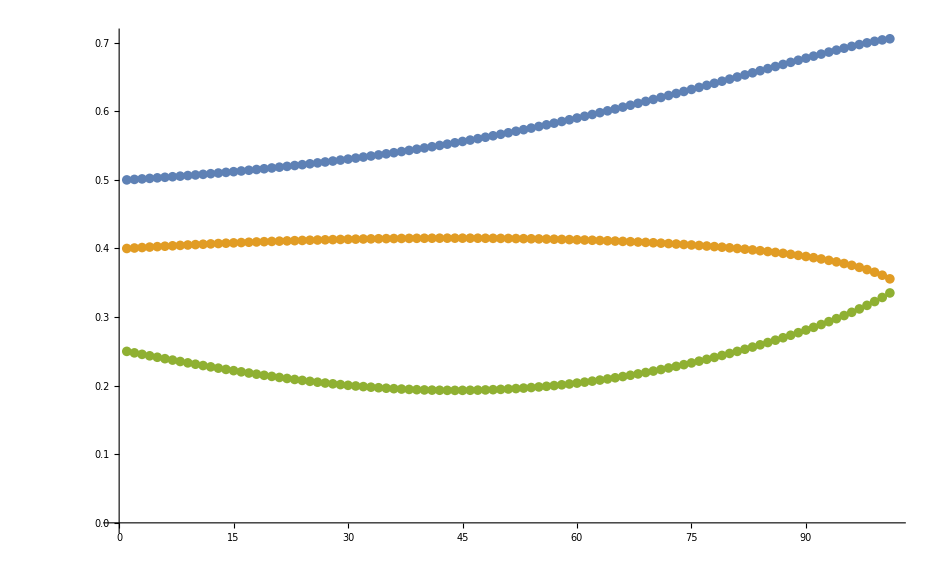

```mathematica
ListPlot[{U[[All,2]],U[[All, 3]],U[[All,4]]}]
```

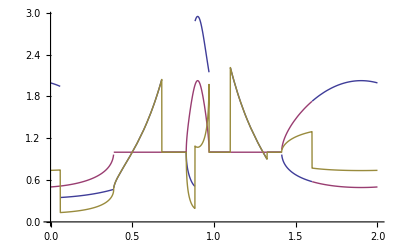

```mathematica
(* first attempt... *)
Subscript[ζ, 1]=Root[80+20 #1^2+#1^4&,1];
Subscript[ζ, 2]=Root[80+20 #1^2+#1^4&,2];
Subscript[ζ, 3]=Root[80+20 #1^2+#1^4&,3];
Subscript[ζ, 4]=Root[80+20 #1^2+#1^4&,4];
Branch=-1;
x=Exp[I Pi a];
Subscript[χ, 1]=5-3 √5+4 √(5-2 √5)+(1+I) 1/x+Subscript[ζ, 2];
Subscript[χ, 2]=45-9 I-(17-7 I) √5-2 √(620-500 I-(285-234 I) √5)-(1+I) Subscript[χ, 1]/x;
Subscript[χ, 3]=10 I-10+(6-2 I) √5+4 √(10-10 ⅈ-(5-4 ⅈ) √5)+(1+I) Subscript[χ, 2]/x;
Subscript[χ, 4]=√5-1+I √2 √(5+√5)+(1+I) Subscript[χ, 3]/x;
Subscript[χ, 5]=(1+I) √(1-√5+Subscript[ζ, 4])-(1-I)( 2 x^2+Conjugate[√Subscript[χ, 4]])-x (1-4 I+√5+Subscript[ζ, 1]);
Subscript[χ, 6]=√5-1-I-√(5-2 √5)+(1- I) x;
y=1/4 Subscript[χ, 5]/Subscript[χ, 6];
z=x/(x-y)((1+I) (-1)^(4/5)-x-y-1+I);
q=1/2((-1)^(1/5)+(-1)^(7/10)-1+I) (1/x-1/y)^-1+Branch/2(1/x-1/y)^-2 √((1/x-1/y)^2(I-1)(2 (-1)^(1/5)+2 (-1)^(7/10)+(1+√5+4I+Subscript[ζ, 2])(1/x+1/y)+(1+I)( 2(1/x+1/y)^2-(-1)^(9/10)+I)));
u=q/x(z x - x y - y z - x^2)/(1+I-(-1)^(3/10)-(-1)^(4/5));
Plot[{Abs[q],Abs[z],Abs[u]},{a,0,2}]
```

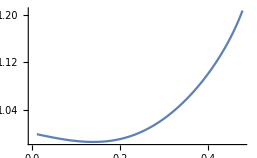
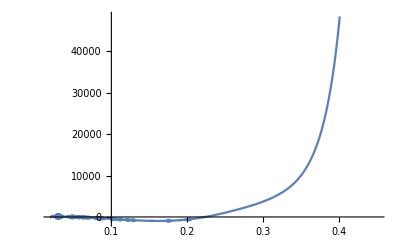
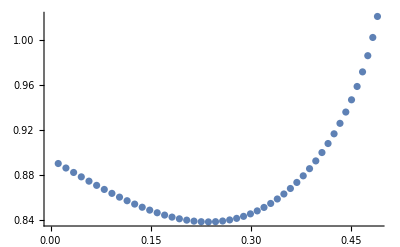
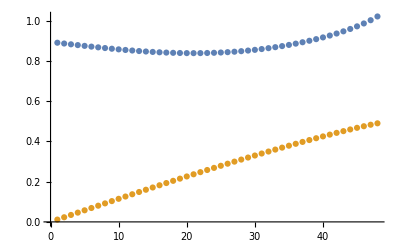
```mathematica
(* interpolation... courtesy of UDEV *)
U={
{0.01,0.998418875596187},{0.011,0.998261391518806},{0.012,0.998104086992416},{0.013,0.997946978348301},{0.014,0.997790081919919},{0.015,0.99763341404311},{0.016,0.99747699105627},{0.017,0.997320829300477},{0.018,0.997164945119699},{0.019,0.997009354860947},{0.02,0.996854074874453},{0.021,0.996699121513782},{0.022,0.996544511136084},{0.023,0.996390260102169},{0.024,0.996236384776671},{0.025,0.996082901528238},
{0.026,0.995929826729649},{0.027,0.995777176757961},{0.028,0.995624967994647},{0.029,0.995473216825769},{0.03,0.995321939642019},{0.031,0.995171152838978},{0.032,0.995020872817101},{0.033,0.994871115981974},{0.034,0.994721898744294},{0.035,0.994573237520114},{0.036,0.994425148730842},{0.037,0.99427764880341},{0.038,0.994130754170321},{0.039,0.993984481269782},{0.04,0.993838846545795},{0.041,0.993693866448202},{0.042,0.993549557432766},{0.043,0.993405935961273},{0.044,0.993263018501577},{0.045,0.99312082152765},{0.046,0.992979361519677},{0.047,0.992838654964023},{0.048,0.992698718353348},{0.049,0.992559568186636},{0.05,0.99242122096915},{0.051,0.992283693212563},{0.052,0.992147001434861},
{0.053,0.992011162160428},
{0.054,0.991876191920041},{0.055,0.991742107250797},{0.056,0.99160892469618},{0.057,0.991476660805988},{0.058,0.991345332136315},{0.059,0.991214955249553},{0.06,0.991085546714259},{0.061,0.99095712310519},{0.062,0.990829701003198},{0.063,0.990703296995162},{0.064,0.990577927673951},{0.065,0.990453609638255},{0.066,0.990330359492578},{0.067,0.990208193847076},{0.068,0.990087129317494},{0.069,0.989967182524992},{0.07,0.98984837009606},{0.071,0.989730708662325},{0.072,0.989614214860486},{0.073,0.989498905332086},{0.074,0.989384796723348},{0.075,0.989271905685046},{0.076,0.989160248872278},{0.077,0.989049842944285},{0.078,0.988940704564242},{0.079,0.988832850399041},{0.08,0.988726297119063},{0.081,0.988621061397973},{0.082,0.988517159912404},{0.083,0.988414609341771},{0.084,0.988313426367965},{0.085,0.988213627675118},{0.086,0.988115229949235},{0.087,0.98801824987798},{0.088,0.987922704150322},{0.089,0.987828609456221},{0.09,0.987735982486329},{0.091,0.987644839931577},{0.092,0.987555198482898},{0.093,0.987467074830825},{0.094,0.987380485665122},{0.095,0.987295447674402},{0.096,0.98721197754573},{0.097,0.98713009196421},{0.098,0.987049807612572},{0.099,0.986971141170741},{0.1,0.986894109315391},

{0.101,0.986818728719495},{0.102,0.986745016051853},{0.103,0.986672987976657},{0.104,0.986602661152921},{0.105,0.98653405223406},{0.106,0.986467177867365},{0.107,0.986402054693448},{0.108,0.986338699345747},{0.109,0.986277128449944},{0.11,0.986217358623458},{0.111,0.986159406474843},{0.112,0.986103288603214},{0.113,0.986049021597697},{0.114,0.985996622036752},{0.115,0.985946106487636},{0.116,0.985897491505747},{0.117,0.985850793633993},{0.118,0.985806029402151},{0.119,0.985763215326213},{0.12,0.985722367907717},{0.121,0.985683503633072},{0.122,0.985646638972863},{0.123,0.98561179038119},{0.124,0.985578974294885},{0.125,0.985548207132867},{0.126,0.985519505295379},{0.127,0.985492885163251},{0.128,0.985468363097154},{0.129,0.985445955436836},{0.13,0.985425678500384},{0.131,0.985407548583377},{0.132,0.985391581958169},{0.133,0.985377794873058},{0.134,0.985366203551482},{0.135,0.985356824191211},{0.136,0.985349672963518},{0.137,0.98534476601235},{0.138,0.985342119453482},{0.139,0.985341749373676},{0.14,0.985343671829819},{0.141,0.985347902848058},{0.142,0.985354458422931},{0.143,0.98536335451649},{0.144,0.985374607057409},{0.145,0.985388231940093},{0.146,0.985404245023784},{0.147,0.98542266213165},{0.148,0.985443499049875},{0.149,0.985466771526743},{0.15,0.985492495271715},

{0.151,0.985520685954504},{0.152,0.985551359204138},{0.153,0.985584530608031},{0.154,0.985620215711034},{0.155,0.985658430014499},{0.156,0.985699188975324},{0.157,0.985742508005011},{0.158,0.985788402468702},{0.159,0.985836887684234},{0.16,0.985887978921176},{0.161,0.985941691399868},{0.162,0.985998040290464},{0.163,0.986057040711971},{0.164,0.986118707731287},{0.165,0.986183056362238},{0.166,0.986250101564617},{0.167,0.986319858243226},{0.168,0.986392341246917},{0.169,0.986467565367631},{0.17,0.986545545339449},{0.171,0.986626295837635},{0.172,0.986709831477687},{0.173,0.986796166814393},{0.174,0.986885316340889},{0.175,0.986977294487723},{0.176,0.987072115621911},{0.177,0.987169794046052},{0.178,0.987270343997333},{0.179,0.987373779646684},{0.18,0.987480115097838},{0.181,0.987589364386437},{0.182,0.987701541479141},{0.183,0.987816660272746},{0.184,0.987934734593304},{0.185,0.988055778195265},{0.186,0.988179804760619},{0.187,0.988306827898053},{0.188,0.988436861142116},{0.189,0.988569917952403},{0.19,0.98870601171274},{0.191,0.988845155730395},{0.192,0.988987363235287},{0.193,0.989132647379228},{0.194,0.989281021235158},{0.195,0.989432497796415},{0.196,0.989587089976006},{0.197,0.989744810605901},{0.198,0.989905672436347},{0.199,0.990069688135187},{0.2,0.990236870287215},

{0.201,0.990407231393527},{0.202,0.990580783870917},{0.203,0.99075754005126},{0.204,0.990937512180977},{0.205,0.991120712420407},{0.206,0.991307152843337},{0.207,0.991496845436458},{0.208,0.991689802098877},{0.209,0.991886034641657},{0.21,0.992085554787359},{0.211,0.992288374169632},{0.212,0.992494504332816},{0.213,0.992703956731566},{0.214,0.992916742730515},{0.215,0.993132873603949},{0.216,0.993352360535523},{0.217,0.993575214617992},{0.218,0.993801446852975},{0.219,0.994031068150753},{0.22,0.994264089330089},{0.221,0.994500521118077},{0.222,0.994740374150028},{0.223,0.994983658969379},{0.224,0.995230386027645},{0.225,0.995480565684384},{0.226,0.995734208207212},{0.227,0.995991323771846},{0.228,0.996251922462172},{0.229,0.996516014270356},{0.23,0.996783609096989},{0.231,0.997054716751261},{0.232,0.997329346951174},{0.233,0.997607509323791},{0.234,0.997889213405522},{0.235,0.998174468642442},{0.236,0.998463284390651},{0.237,0.99875566991667},{0.238,0.999051634397875},{0.239,0.99935118692297},{0.24,0.999654336492499},{0.241,0.999961092019392},{0.242,0.000271462329561821},{0.243,0.000585456162534188},{0.244,0.000903082172113039},{0.245,0.00122434892710169},{0.246,0.00154926491205058},{0.247,0.00187783852805605},{0.248,0.00221007809359537},{0.249,0.00254599184541225},{0.25,0.00288558793943646},{0.251,0.00322887445175263},{0.252,0.00357585937961047},{0.253,0.00392655064248023},{0.254,0.00428095608315253},{0.255,0.00463908346888184},{0.256,0.00500094049257725},{0.257,0.00536653477403765},{0.258,0.00573587386123085},{0.259,0.00610896523162598},{0.26,0.00648581629356186},{0.261,0.00686643438767145},{0.262,0.00725082678835278},

{0.264,0.00803096328496798},{0.265,0.00842672161239547},{0.266,0.00882628271265216},{0.267,0.00922965355265898},{0.268,0.00963684104292486},{0.269,0.0100478520393591},{0.27,0.0104626933451277},{0.271,0.0108813717125685},{0.272,0.0113038938451506},{0.273,0.0117302663994885},{0.274,0.0121604959874064},{0.275,0.0125945891780558},{0.276,0.0130325525000823},{0.277,0.013474392443853},{0.278,0.0139201154637263},{0.279,0.0143697279803846},{0.28,0.0148232363832175},{0.281,0.0152806470327587},{0.282,0.0157419662631795},{0.283,0.0162072003848378},{0.284,0.0166763556868808},{0.285,0.0171494384399105},{0.286,0.0176264548986942},{0.287,0.0181074113049498},{0.288,0.0185923138901704},{0.289,0.0190811688785225},{0.29,0.0195739824897965},{0.291,0.0200707609424159},{0.292,0.0205715104565139},{0.293,0.0210762372570606},{0.294,0.0215849475770645},{0.295,0.0220976476608258},{0.296,0.022614343767261},{0.297,0.0231350421732836},{0.298,0.0236597491772625},{0.299,0.0241884711025263},{0.3,0.024721214300959},{0.301,0.0252579851566405},{0.302,0.0257987900895699},{0.303,0.0263436355594543},{0.304,0.0268925280695672},{0.305,0.0274454741706779},{0.306,0.0280024804650593},{0.307,0.0285635536105609},{0.308,0.0291287003247641},{0.309,0.0296979273892142},{0.31,0.0302712416537225},{0.311,0.0308486500407574},{0.312,0.0314301595499106},{0.313,0.0320157772624471},{0.314,0.0326055103459375},{0.315,0.0331993660589797},{0.316,0.0337973517560042},{0.317,0.034399474892169},

{0.318,0.035005743028347},{0.319,0.0356161638362053},{0.32,0.0362307451033797},{0.321,0.0368494947387473},{0.322,0.0374724207777942},{0.323,0.0380995313880915},{0.324,0.0387308348748684},{0.325,0.0393663396867005},{0.326,0.0400060544212972},{0.327,0.0406499878314063},{0.328,0.0412981488308373},{0.329,0.0419505465005938},{0.33,0.0426071900951313},{0.331,0.043268089048744},{0.332,0.043933252982069},{0.333,0.0446026917087258},{0.334,0.0452764152420955},{0.335,0.0459544338022325},{0.336,0.0466367578229161},{0.337,0.0473233979588601},{0.338,0.0480143650930573},{0.339,0.048709670344294},{0.34,0.0494093250748159},{0.341,0.0501133408981608},{0.342,0.0508217296871609},{0.343,0.051534503582123},{0.344,0.0522516749991864},{0.345,0.0529732566388663},{0.346,0.0536992614947949},{0.347,0.0544297028626552},{0.348,0.0551645943493225},{0.349,0.0559039498822207},{0.35,0.0566477837188918},{0.351,0.057396110456796},{0.352,0.058148945043346},{0.353,0.0589063027861805},{0.354,0.0596681993636914},{0.355,0.0604346508358071},{0.356,0.0612056736550476},{0.357,0.0619812846778541},{0.358,0.0627615011762094},{0.359,0.0635463408495537},{0.36,0.0643358218370106},{0.361,0.0651299627299343},{0.362,0.0659287825847861},{0.363,0.0667323009363585},{0.364,0.0675405378113521},{0.365,0.0683535137423305},{0.366,0.0691712497820491},{0.367,0.0699937675181946},{0.368,0.070821089088531},{0.369,0.0716532371964791},{0.37,0.0724902351271456},{0.371,0.0733321067638153},{0.372,0.0741788766049253},{0.373,0.0750305697815458},{0.374,0.0758872120753805},

{0.375,0.0767488299373142},{0.376,0.0776154505065258},{0.377,0.0784871016301856},{0.378,0.0793638118837797},{0.379,0.0802456105920563},{0.38,0.0811325278506524},{0.381,0.0820245945484104},{0.382,0.0829218423904115},{0.383,0.0838243039217788},{0.384,0.0847320125522493},{0.385,0.0856450025815858},{0.386,0.0865633092258311},{0.387,0.0874869686444649},{0.388,0.0884160179684945},{0.389,0.0893504953295231},{0.39,0.0902904398898333},{0.391,0.0912358918735445},{0.392,0.092186892598884},{0.393,0.0931434845116201},{0.394,0.094105711219724},{0.395,0.0950736175293062},{0.396,0.0960472494818917},{0.397,0.0970266543930978},{0.398,0.0980118808927858},{0.399,0.0990029789667462},{0.4,0.100000000000004},{0.401,0.101002996821823},{0.402,0.102012023752478},{0.403,0.10302713665191},{0.404,0.104048392970331},{0.405,0.105075851800898},{0.406,0.106109573934553},{0.407,0.107149621917143},{0.408,0.108196060108937},{0.409,0.109248954746675},{0.41,0.110308374008265},{0.411,0.111374388080293},{0.412,0.112447069228484},{0.413,0.113526491871272},{0.414,0.114612732656668},{0.415,0.115705870542587},{0.416,0.116805986880851},{0.417,0.117913165505054},{0.418,0.119027492822534},{0.419,0.120149057910673},{0.42,0.121277952617779},{0.421,0.122414271668825},{0.422,0.123558112776382},{0.423,0.124709576756917},{0.424,0.125868767652939},{0.425,0.127035792861345},{0.426,0.128210763268203},{0.427,0.129393793390532},{0.428,0.130585001525467},{0.429,0.131784509907279},{0.43,0.132992444872774},

{0.431,0.134208937035628},{0.432,0.135434121470241},{0.433,0.136668137905765},{0.434,0.137911130930997},{0.435,0.139163250210885},{0.436,0.140424650715477},{0.437,0.141695492962171},{0.438,0.14297594327224},{0.439,0.144266174042672},{0.44,0.145566364034444},{0.441,0.146876698678459},{0.442,0.148197370400496},{0.443,0.149528578966622},{0.444,0.150870531850657},{0.445,0.152223444625446},{0.446,0.153587541379821},{0.447,0.154963055163367},{0.448,0.156350228461265},{0.449,0.157749313701728},{0.45,0.159160573798808},{0.451,0.160584282733603},{0.452,0.1620207261773},{0.453,0.163470202159601},{0.454,0.164933021786879},{0.455,0.166409510014381},{0.456,0.167900006477786},{0.457,0.169404866389545},{0.458,0.170924461506291},{0.459,0.172459181174477},{0.46,0.174009433461836},{0.461,0.17557564638368},{0.462,0.177158269233596},{0.463,0.178757774029799},{0.464,0.180374657089608},{0.465,0.182009440745862},{0.466,0.183662675221776},{0.467,0.185334940681673},{0.468,0.187026849478665},{0.469,0.188739048622788},{0.47,0.190472222495987},{0.471,0.192227095845588},{0.472,0.194004437090856},{0.473,0.195805061984507},{0.474,0.197629837675778},{0.475,0.19947968723068},{0.476,0.201355594673656},{0.477,0.203258610625373},{0.478,0.205189858625474},{0.479,0.207150542244106}
};

ListLinePlot[{V},ImageSize->Full]
-Graphics-
Module[{f=Interpolation[V,InterpolationOrder->20][x],g,h},
g=D[f,{x,5}];
h=Convolve[g,Exp[-100 x^2],x,y];
Print[h];
Plot[{g},{x,0.02,0.45}]]
Convolve[InterpolatingFunction[{{0.01, 0.479}}, <>][x],ⅇ^(-100 x^2),x,y]
-Graphics-
UU={
{0.01,0.998418875596179,0.00579056220190764},{0.02,0.996854074874452,0.0115729625627768},{0.03,0.995321939642019,0.0173390301789874},{0.04,0.993838846545803,0.0230805767271011},{0.05,0.992421220969158,0.0287893895154244},{0.06,0.991085546714251,0.0344572266428719},{0.07,0.98984837009606,0.0400758149519731},{0.08,0.98872629711907,0.0456368514404682},{0.09,0.987735982486329,0.0511320087568382},{0.1,0.986894109315391,0.056552945342308},{0.11,0.98621735862345,0.0618913206882723},{0.12,0.985722367907718,0.0671388160461442},{0.13,0.985425678500385,0.0722871607498109},{0.14,0.985343671829819,0.0773281640850935},{0.15,0.985492495271716,0.0822537523641448},{0.16,0.985887978921176,0.087056010539415},{0.17,0.98654554533945,0.0917272273302782},{0.18,0.987480115097837,0.0962599424510845},{0.19,0.98870601171274,0.100646994143632},{0.2,0.990236870287215,0.104881564856395},{0.21,0.992085554787359,0.108957222606323},{0.22,0.994264089330089,0.112867955334957},{0.23,0.996783609096989,0.116608195451507},{0.24,0.999654336492499,0.120172831753752},{0.25,0.00288558793943698,0.123557206030284},{0.26,0.00648581629356128,0.126757091853221},{0.27,0.0104626933451272,0.129768653327438},{0.28,0.0148232363832176,0.132588381808394},{0.29,0.0195739824897964,0.135213008755103},{0.3,0.0247212143009592,0.137639392849522},{0.31,0.0302712416537224,0.13986437917314},{0.32,0.0362307451033803,0.141884627448311},{0.33,0.0426071900951316,0.143696404952435},{0.34,0.0494093250748159,0.145295337462593},{0.35,0.0566477837188917,0.146676108140555},{0.36,0.064335821837011,0.147832089081495},{0.37,0.0724902351271458,0.148754882436428},{0.38,0.0811325278506527,0.149433736074674},{0.39,0.0902904398898327,0.149854780055084},{0.4,0.100000000000004,0.149999999999998},{0.41,0.110308374008265,0.149845812995868},{0.42,0.121277952617778,0.149361023691112},{0.43,0.132992444872775,0.148503777563613},{0.44,0.145566364034444,0.147216817982778},{0.45,0.159160573798796,0.145419713100602},{0.46,0.174009433461836,0.142995283269082},{0.47,0.190472222495987,0.139763888752007},{0.48,0.209141953105708,0.135429023447146}}
{{0.01,0.998418875596179,0.00579056220190764},{0.02,0.996854074874452,0.0115729625627768},{0.03,0.995321939642019,0.0173390301789874},{0.04,0.993838846545803,0.0230805767271011},{0.05,0.992421220969158,0.0287893895154244},{0.06,0.991085546714251,0.0344572266428719},{0.07,0.98984837009606,0.0400758149519731},{0.08,0.98872629711907,0.0456368514404682},{0.09,0.987735982486329,0.0511320087568382},{0.1,0.986894109315391,0.056552945342308},{0.11,0.98621735862345,0.0618913206882723},{0.12,0.985722367907718,0.0671388160461442},{0.13,0.985425678500385,0.0722871607498109},{0.14,0.985343671829819,0.0773281640850935},{0.15,0.985492495271716,0.0822537523641448},{0.16,0.985887978921176,0.087056010539415},{0.17,0.98654554533945,0.0917272273302782},{0.18,0.987480115097837,0.0962599424510845},{0.19,0.98870601171274,0.100646994143632},{0.2,0.990236870287215,0.104881564856395},{0.21,0.992085554787359,0.108957222606323},{0.22,0.994264089330089,0.112867955334957},{0.23,0.996783609096989,0.116608195451507},{0.24,0.999654336492499,0.120172831753752},{0.25,0.00288558793943698,0.123557206030284},{0.26,0.00648581629356128,0.126757091853221},{0.27,0.0104626933451272,0.129768653327438},{0.28,0.0148232363832176,0.132588381808394},{0.29,0.0195739824897964,0.135213008755103},{0.3,0.0247212143009592,0.137639392849522},{0.31,0.0302712416537224,0.13986437917314},{0.32,0.0362307451033803,0.141884627448311},{0.33,0.0426071900951316,0.143696404952435},{0.34,0.0494093250748159,0.145295337462593},{0.35,0.0566477837188917,0.146676108140555},{0.36,0.064335821837011,0.147832089081495},{0.37,0.0724902351271458,0.148754882436428},{0.38,0.0811325278506527,0.149433736074674},{0.39,0.0902904398898327,0.149854780055084},{0.4,0.100000000000004,0.149999999999998},{0.41,0.110308374008265,0.149845812995868},{0.42,0.121277952617778,0.149361023691112},{0.43,0.132992444872775,0.148503777563613},{0.44,0.145566364034444,0.147216817982778},{0.45,0.159160573798796,0.145419713100602},{0.46,0.174009433461836,0.142995283269082},{0.47,0.190472222495987,0.139763888752007},{0.48,0.209141953105708,0.135429023447146}}
List[##]&[1,2,3]
{1,2,3}
VV[[1]]
{0.01,0.998418875596179,0.00579056220190764}
norm0=(VV[[20]]-VV[[1]])×(VV⟦10⟧-VV⟦1⟧)//Normalize;
norm={√(1/6),-√(1/6),-√(2/3)};
norm0-norm
{-6.367129046225273*^-14,-3.3928415632544784*^-13,1.3777867735598193*^-13}
norm2={0,√(2/3),-√(1/6)}//Normalize;
norm2.norm
norm3={√(2/3),0,√(1/6)}//Normalize;
norm3.norm
0
0
VV=If[#2>.5,List@##,{#1,#2+1,#3}]&@@@UU;
WW=({#.norm3,#.norm2}&)/@VV;
WW//ListPlot
-Graphics-
ListPlot[WW]
-Graphics-
VV=If[#2>.5,List@##,{#1,#2+1,#3}]&@@@UU;
ListPointPlot3D[VV,ImageSize->Large,AxesLabel->{A,B,C}]
-Graphics3D-
```